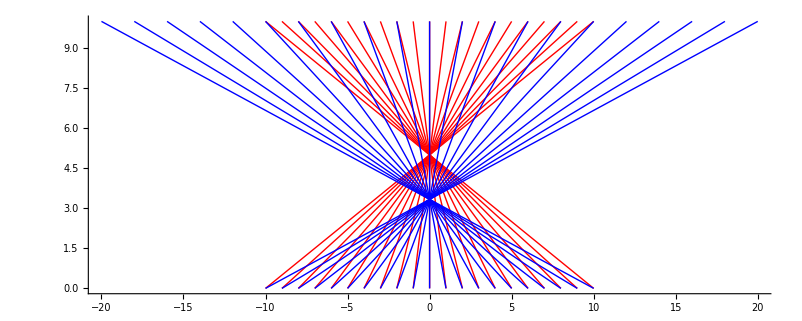

```mathematica
Unset[links];
Unset[rechts];
Unset[a];
links = -10;
rechts = 10;
vx[x_,a_]:=-a (x-links) +a (rechts - x);
Graphics[
{
Map[
{
Red,
Line[#1]
}&,
Table[
{{x,0},{vx[x,0.5],10}},
{x,links,rechts,1}
]
],
Map[
{
Blue,
Line[#1]
}&,
Table[
{{x,0},{vx[x,1],10}},
{x,links,rechts,1}
]
]
},
Axes->True
]
```